# Protein interaction networks

Proteins interact with other proteins in biological processes as varied as DNA replication, signal transduction, movement of molecules into and between cells, and essentially all processes in living cells. In fact, signal transduction, a process in which protein control the signaling into and out of the cell, is key to the study of diseases including many cancers. Their importance in all cellular activity has given rise to active work in the visualization of protein-protein interactions (PPIs). Here, I combined functional constructs, pattern matching, and graph tools to visualize networks of proteins that have a high level of interaction.

Proteins are from the worm Caenorhabditis elegans, a heavily studied organism. The data we used here are from the Center for Cancer Systems Biology at the Dana-Farber Cancer Institute. The data are in the form of a tab-seperated text file (TSV).

Stats of the data

```mathematica
data=Import["http://interactome.dfci.harvard.edu/C_elegans/graphs/sequence_edges/wi2007.txt","TSV"];
```

```mathematica
Length[data]
```

1817

```mathematica
Dimensions[data]
```

{1817,2}

The data are of the form {protein_1, protein_2}, which indicates an interaction between these two named proteins. Before apply the whole analysis to the entire data set, I used Take to obtain the first 12 elements in the data as a prototype data.

```mathematica
Take[data,12]
```

{{#IDA,IDB},{AC3.3,F29G6.3},{AC3.3,R05F9.10},{AC3.3,Y69H2.3},{AC3.7,Y40B10A.2},{B0001.4,F19B6.1},{B0001.7,B0281.5},{B0001.7,F37H8.1},{B0024.10,C06A1.1},{B0024.12,C06E2.1},{B0024.14,B0228.1},{B0024.14,C05G6.1}}

```mathematica
ToEdges[Take[data,12]]
```

```mathematica
{"#IDA"->"IDB","AC3.3"->"F29G6.3","AC3.3"->"R05F9.10","AC3.3"->"Y69H2.3","AC3.7"->"Y40B10A.2","B0001.4"->"F19B6.1","B0001.7"->"B0281.5","B0001.7"->"F37H8.1","B0024.10"->"C06A1.1","B0024.12"->"C06E2.1","B0024.14"->"B0228.1","B0024.14"->"C05G6.1"}
```

```mathematica
edges=ToEdges[Rest[data]];
gr=Graph[edges,GraphStyle->"BasicBlue"]
```

-Graphics-

```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

Select proteins that interacts with at least 12 proteins and graph them

```mathematica
SortBy[Tally[VertexDegree[gr]],First]
```

Tally[VertexDegree[gr]]

```mathematica
Select[VertexList[gr],(VertexDegree[gr,#]>12&)]
```

{R05F9.10,Y69H2.3,Y40B10A.2,DH11.4,K09B11.9,R02F2.5,ZK1053.5,W05H7.4,C18G1.2,T11B7.1,F52E1.7,F46A9.5,Y54E2A.3,ZK858.4,C50F4.1,K12C11.2,C06G1.5,Y65B4BR.4,F32B4.4,ZK849.2,C36C9.1,ZK1055.7,C06A5.9,W09C2.1,F44G3.9,ZK121.2,M04G12.1,T21G5.5,W10C8.2,F01G10.2,Y55F3C.6}

```mathematica
EdgeList[gr]
```

```mathematica
proteins=Select[VertexList[gr],(VertexDegree[gr,#]>12&)]
edges2=Cases[EdgeList[gr],(p1_)];
```

```mathematica
{"R05F9.10","Y69H2.3","Y40B10A.2","DH11.4","K09B11.9","R02F2.5","ZK1053.5","W05H7.4","C18G1.2","T11B7.1","F52E1.7","F46A9.5","Y54E2A.3","ZK858.4","C50F4.1","K12C11.2","C06G1.5","Y65B4BR.4","F32B4.4","ZK849.2","C36C9.1","ZK1055.7","C06A5.9","W09C2.1","F44G3.9","ZK121.2","M04G12.1","T21G5.5","W10C8.2","F01G10.2","Y55F3C.6"}
```

```mathematica
edges2=Cases[EdgeList[gr],(p1_->p2_)/;MemberQ[proteins,p1]&&MemberQ[proteins,p2],Infinity]
```

{C06A5.9->C36C9.1,C06A5.9->DH11.4,C06A5.9->F44G3.9,C06G1.5->DH11.4,C06G1.5->F32B4.4,C06G1.5->K09B11.9,C06G1.5->W05H7.4,C06G1.5->Y54E2A.3,C06G1.5->ZK121.2,C06G1.5->ZK849.2,C36C9.1->K09B11.9,C36C9.1->Y54E2A.3,C36C9.1->Y65B4BR.4,C50F4.1->T21G5.5,C50F4.1->W05H7.4,C50F4.1->Y55F3C.6,C50F4.1->ZK849.2,DH11.4->Y65B4BR.4,DH11.4->Y69H2.3,DH11.4->ZK1053.5,F01G10.2->R02F2.5,F01G10.2->W10C8.2,F01G10.2->Y55F3C.6,F01G10.2->ZK121.2,F32B4.4->F32B4.4,F32B4.4->T11B7.1,F32B4.4->W05H7.4,F32B4.4->W10C8.2,F32B4.4->Y54E2A.3,F32B4.4->Y65B4BR.4,F32B4.4->ZK121.2,K09B11.9->W05H7.4,K12C11.2->K12C11.2,K12C11.2->Y55F3C.6,K12C11.2->ZK858.4,M04G12.1->M04G12.1,M04G12.1->ZK849.2,R02F2.5->W10C8.2,R02F2.5->ZK121.2,R02F2.5->ZK858.4,R05F9.10->R05F9.10,R05F9.10->Y65B4BR.4,T11B7.1->ZK121.2,T21G5.5->T21G5.5,W05H7.4->W05H7.4,W05H7.4->Y65B4BR.4,W05H7.4->ZK121.2,W10C8.2->W10C8.2,Y55F3C.6->Y55F3C.6,Y69H2.3->Y69H2.3,ZK1055.7->ZK1055.7,ZK849.2->ZK849.2,ZK858.4->ZK858.4}

```mathematica
gr1=DeleteCases[edges2,x_->x_]
```

{C06A5.9->C36C9.1,C06A5.9->DH11.4,C06A5.9->F44G3.9,C06G1.5->DH11.4,C06G1.5->F32B4.4,C06G1.5->K09B11.9,C06G1.5->W05H7.4,C06G1.5->Y54E2A.3,C06G1.5->ZK121.2,C06G1.5->ZK849.2,C36C9.1->K09B11.9,C36C9.1->Y54E2A.3,C36C9.1->Y65B4BR.4,C50F4.1->T21G5.5,C50F4.1->W05H7.4,C50F4.1->Y55F3C.6,C50F4.1->ZK849.2,DH11.4->Y65B4BR.4,DH11.4->Y69H2.3,DH11.4->ZK1053.5,F01G10.2->R02F2.5,F01G10.2->W10C8.2,F01G10.2->Y55F3C.6,F01G10.2->ZK121.2,F32B4.4->T11B7.1,F32B4.4->W05H7.4,F32B4.4->W10C8.2,F32B4.4->Y54E2A.3,F32B4.4->Y65B4BR.4,F32B4.4->ZK121.2,K09B11.9->W05H7.4,K12C11.2->Y55F3C.6,K12C11.2->ZK858.4,M04G12.1->ZK849.2,R02F2.5->W10C8.2,R02F2.5->ZK121.2,R02F2.5->ZK858.4,R05F9.10->Y65B4BR.4,T11B7.1->ZK121.2,W05H7.4->Y65B4BR.4,W05H7.4->ZK121.2}

Visualize the PPI graph

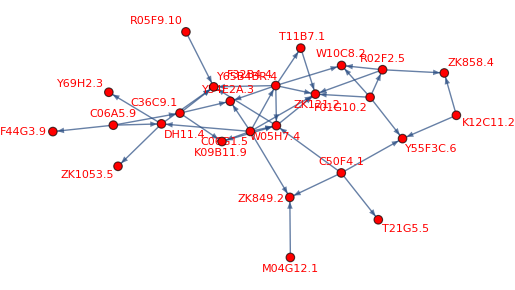

```mathematica
Graph[gr1,VertexStyle->Red,VertexSize->Large,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```

# SchwabeCycle

Sunspots are dark spots on the sun where the surface temperature is reduced by the effects of strong magnetic activity. Extraordinary levels of ultraviolet and x-ray emissions from increased solar activity have pronounced effects on the Earth’s upper atmosphere and so detecting patterns in the frequency of sunspot activity is an important aspect of current solar research. Fortunately, data is available going back to 1818. 

Import data from WDC-SILSO, Royal Observatory of Belgium.

```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["SN_d_tot_V2.0.csv"];
data=Import["SN_d_tot_V2.0.csv","Table","FieldSeparators"->";"]
```

C:\Users\wench\OneDrive - Father Ryan High School\IIT SC

{{1818,1,1,1818.,-1,-1.,0,1},{1818,1,2,1818.,-1,-1.,0,1},{1818,1,3,1818.01,-1,-1.,0,1},{1818,1,4,1818.01,-1,-1.,0,1},{1818,1,5,1818.01,-1,-1.,0,1},{1818,1,6,1818.02,-1,-1.,0,1},73158,{2018,4,26,2018.32,14,1.2,38,0},{2018,4,27,2018.32,14,2.9,25,0},{2018,4,28,2018.32,0,0.,32,0},{2018,4,29,2018.33,0,0.,23,0},{2018,4,30,2018.33,0,0.,31,0}}
 |  |  |  |

Goal: filter all the data and make a plot of the sunspot numbers over the time period covered by the data set. Convert the data to a form that can be used by TimeSeries and DateListPlot:  { {date, value}, ... }.

```mathematica
Length[data]
```

73169

Make a prototype list since the data is toooo long.

```mathematica
test=Part[data,{1,2,3,4,-2,-1}]
```

{{1818,1,1,1818.,-1,-1.,0,1},{1818,1,2,1818.,-1,-1.,0,1},{1818,1,3,1818.01,-1,-1.,0,1},{1818,1,4,1818.01,-1,-1.,0,1},{2018,4,29,2018.33,0,0.,23,0},{2018,4,30,2018.33,0,0.,31,0}}

Filter data

```mathematica
test2=test/.{y_Integer,m_,d_,_Real,sn_Integer,__} :> {DateList[{y,m,d}],sn}
```

{{{1818,1,1,0,0,0.},-1},{{1818,1,2,0,0,0.},-1},{{1818,1,3,0,0,0.},-1},{{1818,1,4,0,0,0.},-1},{{2018,4,29,0,0,0.},0},{{2018,4,30,0,0,0.},0}}

```mathematica
?DateList
```

DateList[] gives the current local date and time in the form {year,month,day,hour,minute,second}. 
DateList[time] gives a date list corresponding to an AbsoluteTime specification.
DateList[date] gives a date list corresponding to a DateObject specification.
DateList[{y,m,d,h,m,s}] converts a date list to standard normalized form. 
DateList[string] converts a date string to a date list. 
DateList[{string,{e,e,…}}] gives the date list obtained by extracting elements "e_i" from "string".

```mathematica
test3=test2/.{lis:{__},sn_/;sn==-1}:>{lis,Missing[]}
```

{{{1818,1,1,0,0,0.},Missing[]},{{1818,1,2,0,0,0.},Missing[]},{{1818,1,3,0,0,0.},Missing[]},{{1818,1,4,0,0,0.},Missing[]},{{2018,4,29,0,0,0.},0},{{2018,4,30,0,0,0.},0}}

```mathematica
?Missing
```

Missing[] represents data that is missing.
Missing[reason] specifies a reason for the data's being missing.
Missing[reason,expr] associates the expression expr with the missing data.

Graph

TimeSeries[…]

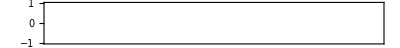

```mathematica
TimeSeries[test3]
DateListPlot[test3,AspectRatio->1/20,Filling->Bottom]
```

```mathematica
?TimeSeries
```

TimeSeries[{{t_1,v_1},{t_2,v_2}…}] represents a time series specified by time-value pairs {t_i,v_i}.
TimeSeries[{v_1,v_2,…},tspec] represents a time series with values v_i at times specified by tspec.

Apply code to the entire data set

```mathematica
data2=data/.{y_Integer,m_,d_,_Real,sn_Integer,__} :> {DateList[{y,m,d}],sn}
data3=data2/.{lis:{__},sn_/;sn==-1}:>{lis,Missing[]}
tsData=TimeSeries[data3]
```

{{{1818,1,1,0,0,0.},-1},{{1818,1,2,0,0,0.},-1},{{1818,1,3,0,0,0.},-1},{{1818,1,4,0,0,0.},-1},{{1818,1,5,0,0,0.},-1},{{1818,1,6,0,0,0.},-1},{{1818,1,7,0,0,0.},-1},{{1818,1,8,0,0,0.},65},{{1818,1,9,0,0,0.},-1},{{1818,1,10,0,0,0.},-1},73149,{{2018,4,21,0,0,0.},28},{{2018,4,22,0,0,0.},22},{{2018,4,23,0,0,0.},23},{{2018,4,24,0,0,0.},22},{{2018,4,25,0,0,0.},18},{{2018,4,26,0,0,0.},14},{{2018,4,27,0,0,0.},14},{{2018,4,28,0,0,0.},0},{{2018,4,29,0,0,0.},0},{{2018,4,30,0,0,0.},0}}
 |  |  |  |

{{{1818,1,1,0,0,0.},Missing[]},{{1818,1,2,0,0,0.},Missing[]},{{1818,1,3,0,0,0.},Missing[]},{{1818,1,4,0,0,0.},Missing[]},{{1818,1,5,0,0,0.},Missing[]},{{1818,1,6,0,0,0.},Missing[]},{{1818,1,7,0,0,0.},Missing[]},{{1818,1,8,0,0,0.},65},{{1818,1,9,0,0,0.},Missing[]},73152,{{2018,4,23,0,0,0.},23},{{2018,4,24,0,0,0.},22},{{2018,4,25,0,0,0.},18},{{2018,4,26,0,0,0.},14},{{2018,4,27,0,0,0.},14},{{2018,4,28,0,0,0.},0},{{2018,4,29,0,0,0.},0},{{2018,4,30,0,0,0.},0}}
 |  |  |  |

TimeSeries[…]

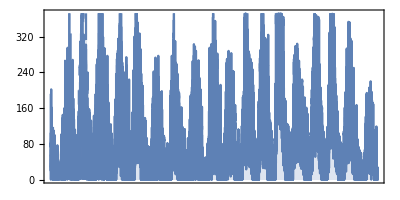

```mathematica
DateListPlot[tsData,AspectRatio->1/2,Filling->Bottom]
```

Data prior to 1849 is not realiable, delete the that data. 
              tsw=TimeSeriesWindow[tsData,{AbsoluteTime[{1849,1,1}],AbsoluteTime[]}]

TemporalData[TimeSeries, <<1>>]

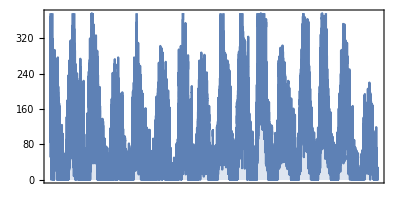

```mathematica
tsw=TimeSeriesWindow[tsData,{AbsoluteTime[{1849,1,1}],AbsoluteTime[]}]
DateListPlot[tsw,AspectRatio->1/2,Filling->Bottom]
```

filter all the noise

```mathematica
24 30 24 30 days hours is just times
```

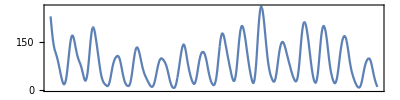

```mathematica
gfData=GaussianFilter[tsw, 24*30];
               DateListPlot[gfData, AspectRatio->1/4]
```

peak

TimeSeries[…]

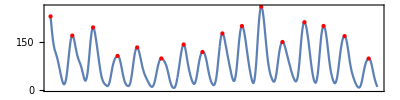

```mathematica
peaks=FindPeaks[gfData,365]
                DateListPlot[{gfData, peaks}, AspectRatio->1/4, Joined->{True, False}, PlotStyle->{Automatic,{Red, PointSize[Medium]}}]
```

```mathematica
{{dates=Map[DateList,peaks["Times"]]}, {□}}
```

{{{{1849,1,1,0,0,0.},{1860,3,29,0,0,0.},{1871,1,18,0,0,0.},{1883,9,19,0,0,0.},{1893,11,14,0,0,0.},{1906,5,24,0,0,0.},{1917,12,16,0,0,0.},{1927,9,8,0,0,0.},{1938,1,1,0,0,0.},{1948,2,11,0,0,0.},{1958,2,5,0,0,0.},{1969,2,13,0,0,0.},{1980,7,2,0,0,0.},{1990,5,24,0,0,0.},{2001,4,16,0,0,0.},{2013,10,9,0,0,0.}}},{□}}

```mathematica
dif=Table[DateDifference[dates[[i]],dates[[i+1]]],{i,1,Length[dates]-1}]
```

{4105. days,3947. days,4627. days,3709. days,4573. days,4224. days,3553. days,3768. days,3693. days,3647. days,4026. days,4157. days,3613. days,3980. days,4559. days}

```mathematica
SchwabeCycle=Mean[dif]
```

4012.07 days

```mathematica
StandardDeviation[dif]
```

361.389 days